```mathematica
Subscript[u, saw][x_]:= Piecewise[{x/9,Mod[x,10]<9},{-(x-10),Mod[x,10]>9}]
```

```mathematica
Subscript[u, par][x_]:= Piecewise[{{(Mod[x,10]-9)^2/81,Mod[x,10]<9},{(Mod[x,10]-9)^2,Mod[x,10]>9}}]
```

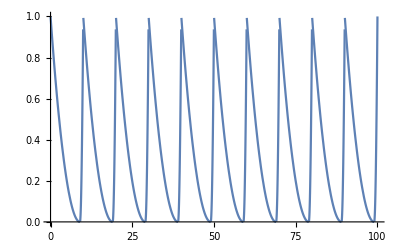

```mathematica
Plot[Subscript[u, par][x],{x,0,100}]
```

```mathematica
Subscript[f, par][x_,y_] := Subscript[u, par][x*10]+Subscript[u, par][y*10]+1/200*(x*10-y*10)^2
```

0.5

1

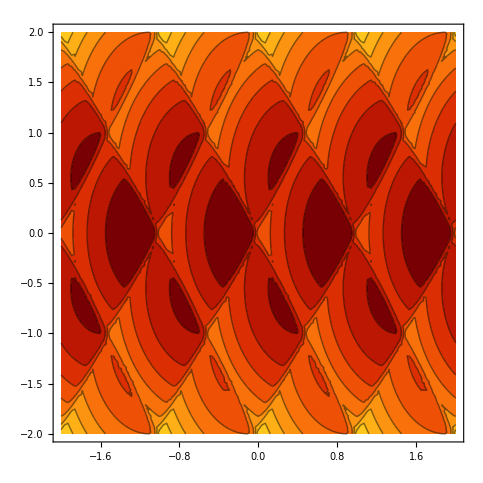

```mathematica
Subscript[T, 1]= 0.5
Subscript[T, 2] = 1
ContourPlot[Subscript[f, par][x-y/2,x+y/2],{x,-2,2},{y,-2,2},Mesh->19,Exclusions->None,ColorFunction->ColorData["SolarColors"]]
```

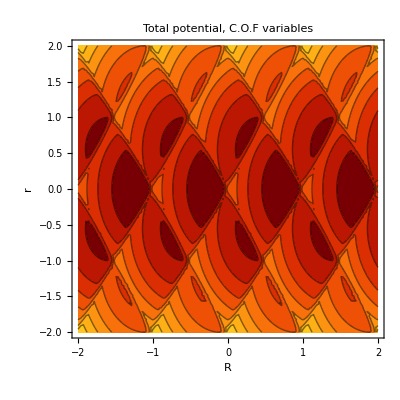

```mathematica
Show[%93,FrameLabel->{{HoldForm[r],None},{HoldForm[R],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"Total"," ","potential"}],","," ",RowBox[{RowBox[{"C",".","O",".","F"}]," ","variables"}]}]],LabelStyle->{GrayLevel[0]}]
```

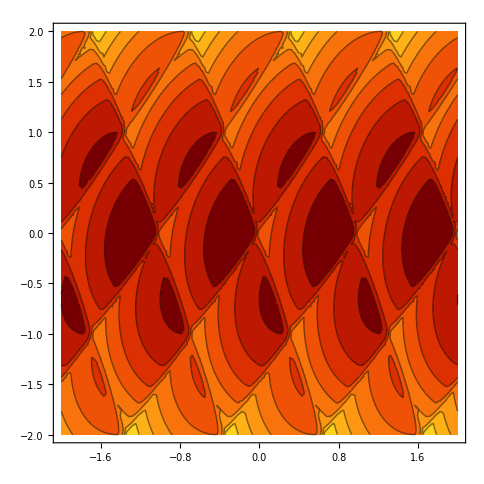

```mathematica
ContourPlot[Subscript[f, par][x-Subscript[T, 2]*y/(Subscript[T, 1]+Subscript[T, 2]),x+Subscript[T, 1]*y/(Subscript[T, 1]+Subscript[T, 2])],{x,-2,2},{y,-2,2},Mesh->19,Exclusions->None,ColorFunction->ColorData["SolarColors"]]
```

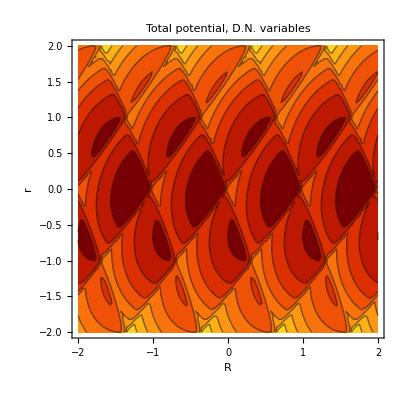

```mathematica
Show[%94,FrameLabel->{{HoldForm[r],None},{HoldForm[R],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"Total"," ","potential"}],","," ",RowBox[{"D",".","N","."," ","variables"}]}]],LabelStyle->{GrayLevel[0]}]
```